```mathematica
NS["schizo_explore"]
```

```mathematica
(* definition of empirical covariance matrix, used a lot in the following *)covmatrix[data_]:=Block[{means=Mean@T@data,numindividuals=Length[data[[1]]]},
((data-means).T[data-means])/numindividuals]
```

```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\nanunana\\data_schizo170727"]
```

C:\Users\pglpm\repositories\nanunana\data_schizo170727

```mathematica
<<"reference_prior.m";
```

```mathematica
fileselect="5"; (* "reduced" *)
categories={"healthy","schizo"};
categoryfiles={"data_con"<>fileselect,"data_schizo"<>fileselect};
numcategories=Length[categories];
origquantities=Flatten@Import["data_params","CSV"];
orignumquantities=Length@origquantities;

Do[tempdata=Import[categoryfiles[[ii]],"CSV"];
(* transform 2nd moments to raw ones *)
Do[tempdata[[jj]]=Sqrt[tempdata[[jj]]+tempdata[[jj-6]]^2],{jj,7,12}];
(* transform 3nd moments to raw ones *)
Do[tempdata[[jj]]=CubeRoot[tempdata[[jj]]+3*tempdata[[jj-6]]*tempdata[[jj-12]]-2*tempdata[[jj-12]]^3],{jj,13,18}];
(* transform 4nd moments to raw ones *)
Do[tempdata[[jj]]=Surd[tempdata[[jj]]+4*tempdata[[jj-6]]*tempdata[[jj-18]]-6*tempdata[[jj-12]]*tempdata[[jj-18]]^2+3*tempdata[[jj-18]]^4,4],{jj,19,24}];

origsubjectfile[ii]=N@tempdata;
numindividuals[ii]=Length[origsubjectfile[ii][[1]]],
{ii,numcategories}];
(* one row for each quantity, one column for each individual *)
minnumindividuals=Min@Table[numindividuals[ii],{ii,numcategories}];
```

```mathematica
Sign[origsubjectfile[3]]//MF
```

Sign[origsubjectfile[3]]

```mathematica
Do[plot=ListPlot[Table[T@origsubjectfile[ii][[{aa,bb},;;]],{ii,numcategories}],PlotRange->All(*{{0,All},{0,All}}*),PlotMarkers->{{○,20},{△,20}},Frame->True,FrameLabel->origquantities[[{aa,bb}]]];
expng["visualize_data2\\expldata-"<>ToString[aa]<>"_"<>ToString[bb],plot];
,{aa,1,23},{bb,aa+1,24}]
```

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;
totaldata=T@totaldata/tempmeans;

(* now renormalize and standardize *)
Do[origsubjectfile[ii]=origsubjectfile[ii]/tempmeans,{ii,numcategories}]

(* renormalize and standardize reference prior parameters *)
(*referencemeans=referencemeans/tempmeans;*)
(*referencecovariance=DiagonalMatrix[1/tempstds].referencecovariance.DiagonalMatrix[1/tempstds];*)
```

```mathematica
Do[data6[ii]=Apply[Times,origsubjectfile[ii]],{ii,numcategories}];
```

```mathematica
data6[1]
```

{244626.,7168.34,9.68854×10^6,711859.,4.73341×10^7,5.82341×10^7,8.94495×10^6,54685.7,1.24251×10^8,1.06785×10^8,1.7335×10^8,1.87828×10^6,6.7696×10^7,833195.,2.95036×10^8,9.93747×10^6,9.73563×10^7,9.92125×10^7,1.97566×10^6,41956.1,5.59753×10^7,2.19786×10^7,448411.,130368.,5.02969×10^6,2.41739×10^6,6.04454×10^7,2.15144×10^6,636.674,4.59457×10^8,293130.,6.49423×10^7,9.91553×10^6,7.91221×10^7,1.70163×10^8,2.4978×10^6,1.25975×10^7,1.67117×10^6,597077.,7.17694×10^6,3.61096×10^7,960153.,4.48767×10^6,1.95236×10^7,1.64894×10^7,2.17698×10^7,1.25463×10^8,7.27029×10^6,183703.,1.86465×10^6,72282.7,1.87009×10^8,2.14974×10^6,3.26406×10^7,1.16934×10^6,8.49728×10^7}

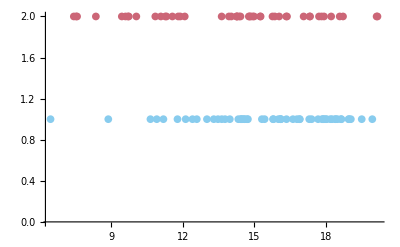

```mathematica
ListPlot[{T@{Log@data6[1],Table[1,numindividuals[1]]},T@{Log@data6[2],Table[2,numindividuals[2]]}}]
```

```mathematica
origsubjectfile[1][[{1,2},;;]]//MF
```

(0.758029 | 0.675088 | 0.852063 | 0.784907 | 0.894786 | 0.903643 | 0.850916 | 0.719425 | 0.917907 | 0.919075 | 0.928697 | 0.808815 | 0.902458 | 0.793282 | 0.944692 | 0.852909 | 0.910941 | 0.9132 | 0.81253 | 0.718038 | 0.896684 | 0.872877 | 0.775716 | 0.743499 | 0.831074 | 0.810508 | 0.899627 | 0.80872 | 0.610898 | 0.95524 | 0.77252 | 0.903004 | 0.848974 | 0.906702 | 0.929063 | 0.820205 | 0.857517 | 0.80165 | 0.779202 | 0.838595 | 0.886659 | 0.799495 | 0.829226 | 0.870926 | 0.864641 | 0.874784 | 0.916878 | 0.843664 | 0.753461 | 0.806436 | 0.730412 | 0.929843 | 0.813457 | 0.882339 | 0.80294 | 0.910465
1.20385 | 1.34973 | 1.04667 | 1.14498 | 0.996083 | 0.987291 | 1.04945 | 1.25684 | 0.969021 | 0.968529 | 0.958027 | 1.10646 | 0.986808 | 1.12969 | 0.941749 | 1.04593 | 0.976813 | 0.974626 | 1.10104 | 1.25342 | 0.992691 | 1.02036 | 1.15724 | 1.2078 | 1.0749 | 1.10333 | 0.99296 | 1.10339 | 1.51264 | 0.930879 | 1.17434 | 0.986587 | 1.05064 | 0.981259 | 0.957721 | 1.09134 | 1.04035 | 1.11743 | 1.14994 | 1.06239 | 1.00459 | 1.12517 | 1.07832 | 1.02366 | 1.03073 | 1.02195 | 0.970134 | 1.05997 | 1.19871 | 1.10993 | 1.24147 | 0.956663 | 1.10186 | 1.00933 | 1.12199 | 0.978566)

```mathematica
plot=ListPlot[Table[T@origsubjectfile[ii][[{1,2},;;]],{ii,numcategories}],PlotRange->Auto(*{{0,All},{0,All}}*),PlotMarkers->{{○,20},{△,20}}];
expng["expldata-1_2",plot];
```

```mathematica
gamma[s_,a_,b_]=Assuming[s>0,FS@PDF[GammaDistribution[a,b],s]]
```

(b^-a ⅇ^(-s/b) s^(-1+a))/Gamma[a]

```mathematica
test1=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[1][[1]],a,b]]]
```

Log[(21620.9 0.0000462515^a b^(-56 a) ⅇ^(-47.0393/b))/Gamma[a]^56]

```mathematica
Integrate[Exp[test1]/(a*b),{a,0,+Infinity},{b,0,+Infinity}]
```

$Aborted

```mathematica
Plot3D[test1-Log[(a*b)],{a,100,500},{b,0.00,0.01},AxesLabel->Auto,PlotPoints->70,PlotRange->{-50,All}]
```

-Graphics3D-

```mathematica
test1=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[1][[2]],a,b]]]
```

Log[(0.0230316 43.4187^a b^(-56 a) ⅇ^(-60.1882/b))/Gamma[a]^56]

```mathematica
max1=NMaximize[{test1,a>0&&b>0},{a,b}]
```

{46.8821,{a→104.595,b→0.0102757}}

```mathematica
test2=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[2][[2]],a,b]]]
```

Log[(0.00270307 369.95^a b^(-48 a) ⅇ^(-54.6605/b))/Gamma[a]^48]

```mathematica
max2=NMaximize[{test2,a>0&&b>0},{a,b}]
```

{29.2594,{a→74.2839,b→0.0153299}}

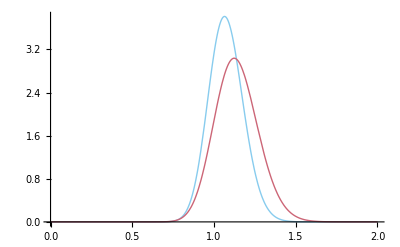

```mathematica
Plot[{gamma[s,a,b]/.max1[[2]],gamma[s,a,b]/.max2[[2]]},{s,0,2},PlotRange->All]
```

```mathematica
Do[test1=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[1][[ii]],a,b]]];
max1=NMaximize[{test1,a>0&&b>0},{a,b}];
test2=Assuming[a>0&&b>0,FS@Total@Log[gamma[origsubjectfile[2][[ii]],a,b]]];
max2=NMaximize[{test2,a>0&&b>0},{a,b}];
plot=Plot[{gamma[s,a,b]/.max1[[2]],gamma[s,a,b]/.max2[[2]]},{s,0,3},PlotRange->All];
expng["mldistr-"<>ToString[ii],plot];,{ii,24}]
```

```mathematica
test1/.{a->150,b->0.0055}
```

64.8990216829

```mathematica
(* improper prior *)
{referencenumber ,referencemeans,referencecovariance}= {0,Table[0,{orignumquantities}],Table[0,{orignumquantities},{orignumquantities}]};
```

```mathematica
fileh=origsubjectfile[1];filea=origsubjectfile[2];
```

```mathematica
minnumindividuals
```

48

```mathematica
orignumquantities
```

24

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[origsubjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;
totaldata=T@totaldata/tempmeans;

(* now renormalize and standardize *)
Do[origsubjectfile[ii]=origsubjectfile[ii]/tempmeans,{ii,numcategories}]

(* renormalize and standardize reference prior parameters *)
referencemeans=referencemeans/tempmeans;
(*referencecovariance=DiagonalMatrix[1/tempstds].referencecovariance.DiagonalMatrix[1/tempstds];*)
```

```mathematica
fileh=origsubjectfile[1];filea=origsubjectfile[3];
```

```mathematica
(* Pareto II distribution, obtained as gamma mixture of exponentials*)par[x_,a_,b_]=PDF[ParetoDistribution[b,a,0],x];
```

```mathematica
(* means and number of samples, for pareto distr *)Do[omeans[ii]=Mean@T[origsubjectfile[ii]];onind[ii]=numindividuals[ii],{ii,numcategories}];
```

```mathematica
(* product of Paretos for the quantities *)ClearAll[prob];
prob[x_,cat_]:=Product[par[x[[ii]],onind[cat],onind[cat]*omeans[cat][[ii]]],{ii,orignumquantities}];
```

```mathematica
Do[
success[cati]=Table[
(*success=0;
avdistr=Table[0,{ii,numcategories}];*)
datum=T[origsubjectfile[cati]][[ii]];
(*Print[datum];
Print[prob[datum,1]];
Print[par[datum[[1]],onind[1],onind[1]*omeans[1][[1]]]];
Print[par[datum[[1]],onind[2],onind[2]*omeans[2][[1]]]];*)
distr=Normalize[Table[prob[datum,jj],{jj,numcategories}],Total]

(*If[Last@Ordering[distr,-1]==cati,++success,Null];
avdistr=avdistr+distr;*)
,{ii,numindividuals[cati]}];
,{cati,2}]
```

```mathematica
success[1]//MF
```

(0.359168 | 0.640832
0.207514 | 0.792486
0.585994 | 0.414006
0.436239 | 0.563761
0.672638 | 0.327362
0.687288 | 0.312712
0.581026 | 0.418974
0.298661 | 0.701339
0.72003 | 0.27997
0.718822 | 0.281178
0.738953 | 0.261047
0.492138 | 0.507862
0.689253 | 0.310747
0.454646 | 0.545354
0.766485 | 0.233515
0.58625 | 0.41375
0.706895 | 0.293105
0.710105 | 0.289895
0.498625 | 0.501375
0.30295 | 0.69705
0.678799 | 0.321201
0.62986 | 0.37014
0.41794 | 0.58206
0.353934 | 0.646066
0.542491 | 0.457509
0.498736 | 0.501264
0.681761 | 0.318239
0.497147 | 0.502853
0.0807556 | 0.919244
0.785185 | 0.214815
0.393291 | 0.606709
0.689022 | 0.310978
0.58124 | 0.41876
0.698014 | 0.301986
0.739114 | 0.260886
0.513411 | 0.486589
0.59711 | 0.40289
0.478592 | 0.521408
0.428477 | 0.571523
0.56207 | 0.43793
0.657179 | 0.342821
0.461711 | 0.538289
0.536502 | 0.463498
0.624175 | 0.375825
0.61274 | 0.38726
0.630131 | 0.369869
0.718775 | 0.281225
0.564819 | 0.435181
0.364238 | 0.635762
0.488236 | 0.511764
0.314266 | 0.685734
0.741438 | 0.258562
0.499333 | 0.500667
0.649468 | 0.350532
0.46896 | 0.53104
0.703152 | 0.296848)

```mathematica
success[2]//MF
```

(0.487098 | 0.512902
0.796201 | 0.203799
0.307786 | 0.692214
0.520412 | 0.479588
0.308004 | 0.691996
0.193296 | 0.806704
0.44818 | 0.55182
0.599311 | 0.400689
0.596046 | 0.403954
0.251474 | 0.748526
0.528335 | 0.471665
0.470695 | 0.529305
0.524226 | 0.475774
0.64986 | 0.35014
0.534673 | 0.465327
0.128635 | 0.871365
0.463731 | 0.536269
0.169864 | 0.830136
0.484905 | 0.515095
0.699169 | 0.300831
0.479881 | 0.520119
0.725322 | 0.274678
0.453497 | 0.546503
0.30029 | 0.69971
0.638617 | 0.361383
0.359968 | 0.640032
0.5644 | 0.4356
0.237093 | 0.762907
0.274857 | 0.725143
0.792037 | 0.207963
0.652214 | 0.347786
0.312578 | 0.687422
0.515835 | 0.484165
0.225526 | 0.774474
0.505115 | 0.494885
0.135236 | 0.864764
0.512818 | 0.487182
0.338841 | 0.661159
0.480119 | 0.519881
0.310366 | 0.689634
0.684023 | 0.315977
0.670276 | 0.329724
0.679709 | 0.320291
0.235531 | 0.764469
0.583726 | 0.416274
0.71724 | 0.28276
0.565494 | 0.434506
0.348523 | 0.651477)

```mathematica
Mean@success[1]
```

{0.555281,0.444719}

```mathematica
Mean@success[2]
```

{0.467938,0.532062}

```mathematica
Det[covmatrix[totaldata]]
```

1.26769×10^-34

```mathematica
rdata=Table[RandomInteger[{-100,100},4],{3}];
```

```mathematica
Det[covmatrix[rdata]]//N
```

1.95436×10^9

```mathematica
(* model comparison by studying P(M|D) ∝ P(D|M). The latter is given by a matrix t-distribution *)
```

```mathematica
subjectfile[1]=filea;subjectfile[2]=filem;subjectfile[3]=fileh;
ClearAll[nindividuals,uu,cc,pp];
Do[nindividuals[ii]=Length[subjectfile[ii][[1]]];uu[ii]=Table[{1},{nindividuals[ii]}];
cc[ii]=IdentityMatrix[nindividuals[ii]]-uu[ii].T[uu[ii]]/(z+nindividuals[ii]);
,{ii,numcategories}];

pp={1,1,1}/3;
```

```mathematica
numquantities=3;setofquantities=Subsets[Range[orignumquantities],{numquantities}];
Length@setofquantities
```

3276

```mathematica
AbsoluteTiming[testcv=ParallelTable[(* cycle through possible graph properties *)
quant=setofquantities[[ll]];crossvalidateall[{filea[[quant]],filem[[quant]],fileh[[quant]]},pp,0]
,{ll, Length@setofquantities},Method->"CoarsestGrained"];]
```

$Aborted

```mathematica
score[data_]:=data[[1,1]]^2*data[[2,1]]*data[[3,1]]^2;ClearAttributes[score,Listable];
```

```mathematica
bestcv=Ordering[score/@testcv[[1;;10]],-2]
```

{7,6}

```mathematica
testcv[[1;;10]]//N
```

{{{0.428571,0.421798},{0.,0.279573},{0.653846,0.342766}},{{0.214286,0.28012},{0.8125,0.473374},{0.307692,0.402347}},{{0.785714,0.550458},{0.,0.289014},{1.,0.999497}},{{0.5,0.323067},{0.1875,0.28157},{0.230769,0.311644}},{{0.714286,0.381832},{0.,0.227961},{0.269231,0.32131}},{{0.5,0.37511},{0.3125,0.352646},{0.269231,0.342054}},{{0.5,0.33938},{0.125,0.255084},{0.423077,0.36248}},{{0.5,0.316384},{0.125,0.277673},{0.269231,0.377671}},{{0.285714,0.362208},{0.625,0.318173},{0.192308,0.325054}},{{0.,0.130455},{0.75,0.485839},{0.346154,0.372663}}}

```mathematica
Listable
```

```mathematica
testcv==testcvp
```

False

```mathematica
Max[testcv-testcvp]
```

0.535392

```mathematica
ClearAll[quant,means,s0];
testresp=ParallelTable[
quant=setofquantities[[ll]];
Exp@Sum[
(* this is for N<d *)
(* 
means[ii]=Mean@T[subjectfile[ii][[quant]]];s0[ii]=T[{means[ii]}].{means[ii]}+IdentityMatrix[numquantities]*nindividuals[ii];

(*nindividuals[ii]*Log[pp[[ii]]]*)
-(nindividuals[ii]/2)*Log[(Pi*Det[s0[ii]]*Exp@Total@Log@Select[Eigenvalues[Inverse[s0[ii]].(covmatrix[subjectfile[ii][[quant]]]*nindividuals[ii])],#>0&])] *)
(* this is for N>d *)
Log[
Product[Gamma[(nindividuals[ii]+1-jj)/2],{jj,numquantities}]/nindividuals[ii]^(numquantities/2)/Det[Pi*covmatrix[subjectfile[ii][[quant]]]*nindividuals[ii]]^(nindividuals[ii]/2)]

,{ii,numcategories}]
,{ll,Length@setofquantities}
,Method->"CoarsestGrained"
];
```

```mathematica
best=Ordering[testresp,-2]
```

{54,1192}

```mathematica
testresp[[best]]
```

{1.78681×10^45,4.54472×10^46}

```mathematica
setofquantities[[best]]
```

{{1,4,7},{4,17,23}}

```mathematica
<<"results_3_4.m";
```

```mathematica
(({resultsa3[[#]],resultsm3[[#]],resultsh3[[#]]})&/@best)//N
```

{{{64.2857,47.0512},{31.25,39.5835},{100.,99.9251}},{{0.,3.54992},{87.5,83.6004},{92.3077,87.7812}}}

```mathematica
<<"crossvalidate.m";
```

```mathematica
selq=setofquantities[[best[[2]]]]
```

{4,17,23}

```mathematica
rea=crossvalidate1[filea[[selq]],{filem[[selq]],fileh[[selq]]},pp,0];
```

```mathematica
Evaluate@Array[re3,3]=crossvalidateall[{filea[[selq]],filem[[selq]],fileh[[selq]]},pp,0];
```

```mathematica
Array[re3,3]*100//N
```

{{0.,3.54992},{87.5,83.6004},{92.3077,87.7812}}

```mathematica
Abort
```

```mathematica
Return
```

```mathematica
(({resultsa4[[#]],resultsm4[[#]],resultsh4[[#]]})&/@best)//N
```

{{{0.,3.58436},{75.,68.8091},{34.6154,39.9044}},{{0.,8.04221},{81.25,76.6917},{96.1538,96.4751}}}

```mathematica
ClearAll[score,prodscore]
```

```mathematica
score[number_]:=If[number[[1]]>perc,number[[2]]^number[[2]],0];
```

```mathematica
perc=100;While[(--perc);
prodscore=(score/@resultsa3)*(score/@resultsm3)*(score/@resultsh3);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
AbsoluteTiming[
aindividuals=Length[origsubjectfile[1][[1]]];
numindividuals[1]=aindividuals-1;
Do[tparameter[ii]=numindividuals[ii]+1-numquantities;,{ii,numcategories}];


resultsh3=ParallelTable[(* cycle through possible graph properties *)
quant=setofquantities[[ll]];

Do[means[ii]=Mean@T[origsubjectfile[ii][[quant]]];
tmatrix[ii]=covmatrix[origsubjectfile[ii][[quant]]]*(numindividuals[ii]+1)/tparameter[ii];
,{ii,2,numcategories}];

mainfile=origsubjectfile[1][[quant]];

hits=totpr=0;
Do[(* cycle through individuals in first group *)
datax=T[mainfile][[ndat]];
secondfile=T[Drop[T[mainfile],{ndat}]];
means[1]=Mean@T[secondfile];
tmatrix[1]=covmatrix[secondfile]*(numindividuals[1]+1)/tparameter[1];

distr=Normalize[(* Normalize is faster *)Table[1/3*PDF[MultivariateTDistribution[means[ii],tmatrix[ii],tparameter[ii]],datax],{ii,numcategories}],Total];

If[Last@Ordering[distr,-1]==1,++hits,Null];
totpr=totpr+distr[[1]];

,{ndat,aindividuals}];

100*{hits,totpr}/aindividuals

,{ll,Length@setofquantities},Method->"CoarsestGrained"];
]
```

{50.017,Null}

```mathematica
(* some analysis shows that selecting eigenvector seems to be a bad idea *)eigenvectors=T[Eigenvectors[covmatrix[totaldata]]];
ieigenvectors=Inverse[eigenvectors];

Do[origsubjectfile[ii]=ieigenvectors.origsubjectfile[ii],{ii,numcategories}];
totaldata=ieigenvectors.totaldata;

referencemeans=ieigenvectors.referencemeans;
referencecovariance=ieigenvectors.referencecovariance.eigenvectors;
```

```mathematica
(* we can use at most (num.subjects -2) quantities. We choose those that have the covariance matrix with largest volume *)

(* this selects all possible subsets of (num.subjs-2) quantities out of all available quantities *)
(*numusedquantities=minnumindividuals-2;*)
numusedquantities=24;

trialquantities=Subsets[Range[orignumquantities],{numusedquantities}];
totcovmatrix=covmatrix[totaldata];

(* this calculates all determinants of cov. matrices for these subsets *)
trialdeterminants=Table[Abs@Det[totcovmatrix[[ii,ii]]],{ii,trialquantities}];

(* this is the subset with largest scatter *)
bestquantities=Ordering[trialdeterminants,-1][[1]];
chosenquantities=trialquantities[[bestquantities]];
ClearAll[trialquantities,trialdeterminants];
origquantities[[chosenquantities]]
```

{graphweights1, shortest path1, cluster coeff.1, weighted degree1, normalized weighted degree1, closeness centrality1, graphweights2, shortest path2, cluster coeff.2, weighted degree2, normalized weighted degree2, closeness centrality2, graphweights3, shortest path3, cluster coeff.3, weighted degree3, normalized weighted degree3, closeness centrality3, graphweights4, shortest path4, cluster coeff.4, weighted degree4, normalized weighted degree4, closeness centrality4}

```mathematica
relevant={1,2,3,8,9,12,15,16,20,21,23,24}
```

{1,2,3,8,9,12,15,16,20,21,23,24}

```mathematica
chosenquantities=relevant
```

{1,2,3,8,9,12,15,16,20,21,23,24}

```mathematica
chosenquantities={1,2,3,7,10,13,14,18,19,21,22};
```

```mathematica
qqq=Sort@RandomSample[relevant,3];Print[qqq];
ListPointPlot3D[Evaluate@Table[origsubjectfile[ii][[qqq]],{ii,3}],BoxRatios->1,PlotStyle->{{PointSize[Large],red},{PointSize[Large],blue},{PointSize[Large],green}},PlotRange->All,ViewPoint->Dynamic[viewpoint],AxesLabel->myaxes[origquantities[[qqq]]]]
```

```mathematica
expng["discrete_quantities"]
```

./discrete_quantities.png

```mathematica
(* select subsets of data, for each category, corresponding to the optimal quantities *)
quantities=origquantities[[chosenquantities]];numquantities=Length@quantities;
Do[subjectfile[ii]=origsubjectfile[ii][[chosenquantities]],{ii,numcategories}];

nreferencemeans=referencemeans[[chosenquantities]];
nreferencecovariance=referencecovariance[[chosenquantities,chosenquantities]];
```

```mathematica
Do[means[ii]=Mean@T@subjectfile[ii];
tparameter[ii]=numindividuals[ii]+1-numquantities;
tcovariance[ii]=covmatrix[ subjectfile[ii]];
,{ii,numcategories}];
```

```mathematica
orde=Ordering[Product[Abs@Diagonal[covmatrix[origsubjectfile[ii]]],{ii,numcategories}],8]
```

{4,21,16,15,22,18,24,9}

```mathematica
numtry=RandomSample[Range[orignumquantities],8];
```

```mathematica
Do[omeans[ii]=Mean[T[origsubjectfile[ii]]];ocovm[ii]=Symmetrize@covmatrix[origsubjectfile[ii]];,{ii,numcategories}]
```

```mathematica
Array[omeans,3]//T//MF
```

(-0.375824 | -0.0672789 | 0.243769
0.547065 | 0.04255 | -0.320758
-0.283451 | -0.100243 | 0.214315
0.360124 | 0.801578 | -0.687192
-0.0148227 | -0.176416 | 0.116545
-0.377064 | -0.0947126 | 0.261319
-0.232532 | -0.0735923 | 0.170497
0.502016 | -0.0303538 | -0.251637
0.208745 | -0.183399 | 0.000459583
-0.151903 | -0.141906 | 0.169121
0.218832 | -0.389348 | 0.121766
0.0642604 | -0.101096 | 0.0276111
-0.0449675 | 0.0932653 | -0.0331808
-0.283438 | 0.0381687 | 0.129132
-0.366819 | 0.170934 | 0.0923281
-0.120383 | -0.188291 | 0.180693
0.0667007 | -0.259964 | 0.124062
0.334983 | -0.211461 | -0.0502454
-0.114415 | 0.0379939 | 0.0382272
0.439699 | -0.0975029 | -0.176759
0.372862 | -0.15382 | -0.106114
-0.138748 | -0.123718 | 0.150845
0.0445739 | -0.345985 | 0.188912
0.311777 | -0.140375 | -0.0814952)

```mathematica
vector=Array[x,2];
```

```mathematica
intb=ReplacePart[Table[{x[ii],-Infinity,+Infinity},{ii,2}],0->Sequence]
```

Sequence[{x[1],-∞,∞},{x[2],-∞,∞}]

```mathematica
NIntegrate[Product[PDF[MultinormalDistribution[omeans[ii],ocovm[ii]],vector],{ii,numcategories}],Evaluate@intb,PrecisionGoal->2,AccuracyGoal->Infinity,MinRecursion->20,MaxRecursion->20]
```

$Aborted

```mathematica
Product[PDF[MultinormalDistribution[omeans[ii][[{2}]],ocovm[ii][[{2},{2}]]],{x}],{ii,numcategories}]
```

0.075244 ⅇ^(-0.3953 (-0.547065+x)^2-0.655943 (-0.04255+x)^2-0.677018 (0.320758+x)^2)

```mathematica
Mod[3,3]+1
```

1

```mathematica
numusedquantities=3;

trialquantities=Subsets[Range[orignumquantities],{numusedquantities}];
```

```mathematica
vector=Array[x,numusedquantities];intb=ReplacePart[Table[{x[ii],-Infinity,+Infinity},{ii,numusedquantities}],0->Sequence] ;overl=Table[inte=NIntegrate[Product[PDF[MultinormalDistribution[omeans[ii][[ll]],ocovm[ii][[ll,ll]]],vector],{ii,numcategories}],Evaluate@intb,PrecisionGoal->1,AccuracyGoal->+Infinity];Print[ll,inte];inte,{ll,trialquantities}];
```

$Aborted

```mathematica
NIntegrate[Product[PDF[MultinormalDistribution[omeans[ii][[{16,18,22}]],ocovm[ii][[{16,18,22},{16,18,22}]]],vector],{ii,numcategories}],Evaluate@intb,PrecisionGoal->1,AccuracyGoal->+Infinity,WorkingPrecision->30]
```

0.256235251781658096449378647753

```mathematica
overl[[1;;10]]
```

{0.0515084,0.,0.00363415,0.172348,0.0253653,0.0335705,0.00624655,0.00640976,0.0028607,0.00820197}

```mathematica
Ordering[overl,9]
```

{2,23,44,45,46,47,48,49,50}

```mathematica
trialquantities[[45]]
```

{1,4,6}

```mathematica
chosenquantities=Union@Flatten@trialquantities[[Ordering[overl,2]]]
```

{1,2,3,4}

```mathematica
mnumind[1]=pnumind[1]-1;
mmean[1]=(pnumind[1]*pmean[1]-datax)/mnumind[1];
mcovmatr[1]=Symmetrize[(pnumind[1]*pcovmatr[1]-(T[{mmean[1]-datax}].{mmean[1]-datax})*mnumind[1]/pnumind[1])/mnumind[1]];
```

```mathematica
numquantities=4;setofquantities=Subsets[Range[orignumquantities],{numquantities}];
```

```mathematica
Length[setofquantities]
```

20475

```mathematica
origsubjectfile[3]=filea;origsubjectfile[2]=filem;origsubjectfile[1]=fileh;
Do[numindividuals[ii]=Length[origsubjectfile[ii][[1]]];,{ii,numcategories}];
```

```mathematica
AbsoluteTiming[
aindividuals=Length[origsubjectfile[1][[1]]];
numindividuals[1]=aindividuals-1;
Do[tparameter[ii]=numindividuals[ii]+1-numquantities;,{ii,numcategories}];


resultsh4=ParallelTable[(* cycle through possible graph properties *)
quant=setofquantities[[ll]];

Do[means[ii]=Mean@T[origsubjectfile[ii][[quant]]];
tmatrix[ii]=covmatrix[origsubjectfile[ii][[quant]]]*(numindividuals[ii]+1)/tparameter[ii];
,{ii,2,numcategories}];

mainfile=origsubjectfile[1][[quant]];

hits=totpr=0;
Do[(* cycle through individuals in first group *)
datax=T[mainfile][[ndat]];
secondfile=T[Drop[T[mainfile],{ndat}]];
means[1]=Mean@T[secondfile];
tmatrix[1]=covmatrix[secondfile]*(numindividuals[1]+1)/tparameter[1];

distr=Normalize[(* Normalize is faster *)Table[1/3*PDF[MultivariateTDistribution[means[ii],tmatrix[ii],tparameter[ii]],datax],{ii,numcategories}],Total];

If[Last@Ordering[distr,-1]==1,++hits,Null];
totpr=totpr+distr[[1]];

,{ndat,aindividuals}];

100*{hits,totpr}/aindividuals

,{ll,Length@setofquantities},Method->"CoarsestGrained"];
]
```

{532.729,Null}

```mathematica
Max[resultsa4[[;;,1]]]//N
```

92.8571

```mathematica
Max[resultsm4[[;;,1]]]//N
```

100.

```mathematica
Max[resultsh4[[;;,1]]]//N
```

100.

```mathematica
Save["results_3_4.m",{resultsa3,resultsm3,resultsh3,resultsa4,resultsm4,resultsh4}];
```

```mathematica
ClearAll[score,prodscore]
```

```mathematica
score[number_]:=If[number[[1]]>perc,number[[2]]^number[[2]],0];
```

```mathematica
perc=100;While[(--perc);
prodscore=(score/@resultsa4)*(score/@resultsm4)*(score/@resultsh4);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
perc
```

64

```mathematica
best3=Ordering[prodscore,-2]
```

{8515,3395}

```mathematica
{resultsa4,resultsm4,resultsh4}[[;;,best,;;]]//N
```

{{{64.2857,48.4086},{64.2857,57.6419}},{{68.75,57.9062},{68.75,56.1796}},{{100.,99.6817},{96.1538,95.5082}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best]]
```

{{ weighted degree1, closeness centrality1, normalized weighted degree4, mean across time},{ shortest path1, weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
{resultsa4,resultsm4,resultsh4}[[;;,best3,;;]]//N
```

{{{64.2857,48.4086},{64.2857,57.6419}},{{68.75,57.9062},{68.75,56.1796}},{{100.,99.6817},{96.1538,95.5082}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best3]]
```

{{ weighted degree1, closeness centrality1, normalized weighted degree4, mean across time},{ shortest path1, weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
(* three *)
```

```mathematica
aindividuals
```

16

```mathematica
numquantities=3;setofquantities=Subsets[Range[orignumquantities],{numquantities}];
```

```mathematica
Length[setofquantities]
```

3276

```mathematica
setofquantities={relevant};numquantities=Length[setofquantities[[1]]]
```

12

```mathematica
setofquantities={RandomSample[Range[orignumquantities],12]};
numquantities=Length[setofquantities[[1]]]
```

12

```mathematica
origsubjectfile[1]=filea;origsubjectfile[2]=filem;origsubjectfile[3]=fileh;
Do[numindividuals[ii]=Length[origsubjectfile[ii][[1]]];,{ii,numcategories}];
```

```mathematica
AbsoluteTiming[
ClearAll[hits];
aindividuals=Length[origsubjectfile[1][[1]]];
numindividuals[1]=aindividuals-1;
Do[tparameter[ii]=numindividuals[ii]+1-numquantities;,{ii,numcategories}];


results3[1]=ParallelTable[(* cycle through possible graph properties *)
Block[{hits},quant=setofquantities[[ll]];

Do[means[ii]=Mean@T[origsubjectfile[ii][[quant]]];
tmatrix[ii]=covmatrix[origsubjectfile[ii][[quant]]]*(numindividuals[ii]+1)/tparameter[ii];
,{ii,2,numcategories}];

mainfile=origsubjectfile[1][[quant]];

hits[1]=0;hits[2]=0;hits[3]=0;totpr=0;
Do[(* cycle through individuals in first group *)
datax=T[mainfile][[ndat]];
secondfile=T[Drop[T[mainfile],{ndat}]];
means[1]=Mean@T[secondfile];
tmatrix[1]=covmatrix[secondfile]*(numindividuals[1]+1)/tparameter[1];

distr=Normalize[(* Normalize is faster *)Table[1/3*PDF[MultivariateTDistribution[means[ii],tmatrix[ii],tparameter[ii]],datax],{ii,numcategories}],Total];

++(hits[Last@Ordering[distr,-1]]);
totpr=totpr+distr;

,{ndat,aindividuals}];

{Array[hits,3],totpr}/aindividuals]

,{ll,Length@setofquantities},Method->"CoarsestGrained"];
]
```

{30.706,Null}

```mathematica
Min[results3[1][[;;,1,1]]]//N
```

0.

```mathematica
results3[1]*100//N
```

{{{7.14286,78.5714,14.2857},{7.95794,75.8653,16.1767}}}

```mathematica
Binomial[28,12]
```

30421755

```mathematica
Max[results3[1][[;;,2,1]]]//N
```

0.833256

```mathematica
Ordering[results3[1][[;;,1,1]],1]
```

{15}

```mathematica
results3[1][[15]]*100//N
```

{{0.,85.7143,14.2857},{8.88721,68.0531,23.0597}}

```mathematica
se
```

```mathematica
Max[resultsm3[[;;,1]]]//N
```

100.

```mathematica
origquantities[[setofquantities[[15]]]]
```

{graphweights1, shortest path1, cluster coeff.3}

```mathematica
chosenquantities={1,2,3,7,10,13,14,18,19,21,22};
```

```mathematica
qqq=setofquantities[[15]];
ListPointPlot3D[Evaluate@Table[origsubjectfile[ii][[qqq]],{ii,3}],BoxRatios->1,PlotStyle->{{PointSize[Large],red},{PointSize[Large],blue},{PointSize[Large],green}},PlotRange->All,ViewPoint->Dynamic[viewpoint],AxesLabel->myaxes[origquantities[[qqq]]]]
```

-Graphics3D-

```mathematica
expng["discrete_quantities"]
```

./discrete_quantities.png

```mathematica
Max[resultsh3[[;;,1]]]//N
```

100.

```mathematica
score[datum_]:=datum[[1,1]];score3[datum_]:=datum[[1,1]]^3;
```

```mathematica
prodscore=(score3/@results3[1])*(score/@results3[2])*(score3/@results3[3]);
```

```mathematica
best=Ordering[prodscore,-2]
```

{1119,1170}

```mathematica
Table[results3[ii][[1200]],{ii,3}]*100//N
```

{{{92.8571,7.14286,0.},{70.3447,29.6553,1.20625×10^-30}},{{31.25,68.75,0.},{46.961,53.039,4.66608×10^-34}},{{96.1538,0.,3.84615},{91.1279,3.25304,5.61911}}}

```mathematica
Table[results3[ii][[1170]],{ii,3}]*100//N
```

{{{85.7143,14.2857,0.},{83.3256,16.6744,6.43593×10^-20}},{{56.25,43.75,0.},{58.4382,41.5618,7.2857×10^-24}},{{92.3077,0.,7.69231},{87.5696,4.13524,8.29517}}}

```mathematica
ClearAll[score,prodscore]
```

```mathematica
score[number_]:=If[number[[1]]>perc,number[[2]]^number[[2]],0];
```

```mathematica
perc=100;While[(--perc);
prodscore=(score/@resultsa3)*(score/@resultsm3)*(score/@resultsh3);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
perc
```

64

```mathematica
best3=Ordering[prodscore,-2]
```

{3276,1146}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,best,;;]]//N
```

{{{0.,10.1529},{64.2857,54.3523}},{{56.25,47.8663},{68.75,59.8564}},{{69.2308,56.7981},{96.1538,94.7381}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best]]
```

{{ closeness centrality4, mean across time, std across time},{ weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,best3,;;]]//N
```

{{{0.,10.1529},{64.2857,54.3523}},{{56.25,47.8663},{68.75,59.8564}},{{69.2308,56.7981},{96.1538,94.7381}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best3]]
```

{{ closeness centrality4, mean across time, std across time},{ weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
Ordering[resultsa3,-2]
```

{1170,1200}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,%,;;]]//N
```

{{{85.7143,83.3256},{92.8571,70.3447}},{{56.25,58.4382},{31.25,46.961}},{{92.3077,87.5696},{96.1538,91.1279}}}

```mathematica
origquantities[[#]]&/@setofquantities[[%%]]
```

{{ weighted degree1, graphweights3, weighted degree4},{ weighted degree1, weighted degree3, graphweights4}}

```mathematica
ClearAll[score,prodscore];score[number_]:=number[[1]];
score2[number_]:=number[[2]]^2;
```

```mathematica
perc=100;While[(--perc);
prodscore=(score2/@resultsa4)*(score/@resultsm4)*(score2/@resultsh4);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
prodscore=(score2/@resultsa4)*(score/@resultsm4)*(score2/@resultsh4);
```

```mathematica
Ordering[prodscore,-2]
```

{8951,3419}

```mathematica
{resultsa4,resultsm4,resultsh4}[[;;,%,;;]]//N
```

{{{85.7143,78.3422},{92.8571,82.2203}},{{62.5,60.6178},{62.5,57.7674}},{{96.1538,95.3746},{96.1538,95.7878}}}

```mathematica
setofquantities=Subsets[Range[orignumquantities],{4}];origquantities[[#]]&/@setofquantities[[%526]]
```

{{ weighted degree1, shortest path2, graphweights3, weighted degree4},{ shortest path1, weighted degree1, graphweights3, weighted degree4}}

```mathematica
setofquantities[[%526]]
```

{{4,10,15,24},{2,4,15,24}}

```mathematica
setofquantities[[2]]
```

{1}

```mathematica
(* general average test inferring one datum from all the rest *)
ClearAll[sample,prob,distr,distr2];
testminusonedata[dataall_,ind_,numsamples_:10000]:=
(
precision=Auto;
pp={1,1,1}/3;
numcat=Length[dataall];
numquant=Length[dataall[[1]]];
maindata=dataall[[1]];

(* full data for cat. 1 *)
tempnum=(individuals=Length[maindata[[1]]]);
tempmean=Mean@T[maindata];
pnumind[1]=tempnum;
pmean[1]=tempmean;
pcovmatr[1]=Symmetrize[covmatrix[maindata]];

Do[(* data for other categories without the additional datum *)
dmaindata=dataall[[ii]];
tempnum=Length[dmaindata[[1]]];
tempmean=Mean@T[dmaindata];
mnumind[ii]=tempnum;
mmean[ii]=tempmean;
mcovmatr[ii]=Symmetrize[covmatrix[dmaindata]];
,{ii,2,numcat}];

datax=Flatten[T[maindata][[ind]]];

(* find sufficient statistics minus eliminated datum in first cat. *)
mnumind[1]=pnumind[1]-1;
mmean[1]=(pnumind[1]*pmean[1]-datax)/mnumind[1];
mcovmatr[1]=Symmetrize[(pnumind[1]*pcovmatr[1]-(T[{mmean[1]-datax}].{mmean[1]-datax})*mnumind[1]/pnumind[1])/mnumind[1]];

Do[(* find suff. statistics for other categories plus extra datum *)
pnumind[ii]=mnumind[ii]+1;
pmean[ii]=(mnumind[ii]*mmean[ii]+datax)/pnumind[ii];
pcovmatr[ii]=Symmetrize[(
mnumind[ii]*mcovmatr[ii]+
(T[{mmean[ii]-datax}].{mmean[ii]-datax})*
mnumind[ii]/pnumind[ii])/pnumind[ii]];
,{ii,2,numcat}];

(* distribution to sample the Normal-Inv-Wishart prior from *)
distr=Table[pp[[ii]]*PDF[MultivariateTDistribution[mmean[ii],mcovmatr[ii]*(mnumind[ii]+1)/(mnumind[ii]+1-numquant),mnumind[ii]+1-numquant],datax],{ii,numcategories}];distr=distr/Total[distr];

newsample=Table[(* create samples for prior parameters *)
kk=RandomChoice[distr->Range[numcat]];

Do[(* the non-selected is has prob. conditional on data minus the extra datum *)
svar[ii]=RandomVariate[InverseWishartMatrixDistribution[mnumind[ii],mcovmatr[ii]*mnumind[ii]],WorkingPrecision->precision];
smean[ii]=RandomVariate[MultinormalDistribution[mmean[ii],svar[ii]/mnumind[ii]],WorkingPrecision->precision];

,{ii,Drop[Range[numcat],{kk}]}];

(* the selected is has prob. conditional on data plus the extra datum *)
svar[kk]=RandomVariate[InverseWishartMatrixDistribution[pnumind[kk],pcovmatr[kk]*pnumind[kk]],WorkingPrecision->precision];
smean[kk]=RandomVariate[MultinormalDistribution[pmean[kk],svar[kk]/pnumind[kk]],WorkingPrecision->precision];

(* construct probability vector for categories with the parameters just sampled *)
distr2=Table[pp[[ii]]*PDF[MultinormalDistribution[smean[ii],svar[ii]],datax],{ii,numcat}];
distr2=distr2/Total[distr2]

,{numsamples}];

{distr,newsample}

);
```

```mathematica
{proba,sample}=testminusonedata[{filea[[{2,4,15,24},;;]],filem[[{2,4,15,24},;;]],fileh[[{2,4,15,24},;;]]},14,1000];
```

```mathematica
viewpointh={-2.158703721114823,-2.3659285575604585,1.0919616774250367};
```

```mathematica
histbins=Append[Table[ii,{ii,0,1-1/10,1/10}],1001/1000]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1001/1000}

```mathematica
Mean[sample]
```

{0.988933,0.0110666,6.13102295794426×10^-29043}

```mathematica
sample[[1;;10]]
```

{{0.999999,1.41009×10^-6,1.49650813469701×10^-56225},{1.,6.61779×10^-8,1.18365291575311×10^-63905},{0.999784,0.00021564,1.69014342418627×10^-61138},{0.999999,5.27169×10^-7,1.1865356685814×10^-91171},{0.999432,0.000567981,2.33689663547576×10^-53556},{1.,5.77374×10^-19,9.71100208850502×10^-76183},{1.,1.71676×10^-9,3.07868241491358×10^-65952},{0.99998,0.0000195691,6.86827398741379×10^-73022},{1.,3.33504×10^-9,7.24177841156426×10^-149172},{1.,8.15755×10^-8,6.65736940733134×10^-67426}}

```mathematica
proba
```

{0.986547,0.0134533,1.19302×10^-52}

```mathematica
Do[{proba,sample}=testminusonedata[{filea[[{2,4,15,24},;;]],filem[[{2,4,15,24},;;]],fileh[[{2,4,15,24},;;]]},indi,500];
sample=sample[[;;,{1,2,3}]];proba=proba[[{1,2,3}]];
Print[indi,Chop@proba*100,Chop@Mean[sample]*100];
his=Histogram3D[Chop[sample[[;;,{2,1}]]],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1.01},{0,1.01},{0,All}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{Subscript[p,MCI],Subscript[p,AD],P[p]}],PlotLabel->mylabels[{P[A,M,H]==Chop[proba]*100}],ViewPoint->Dynamic[viewpointh]];
expng["hist_AD_ind"<>ToString[indi],his];,{indi,14}]
```

```mathematica
(* All quantities *)
numquantities=12;setofquantities=Subsets[Range[orignumquantities],{numquantities}];
```

```mathematica
Length[setofquantities]
```

1

```mathematica
origsubjectfile[1]=filea;origsubjectfile[2]=filem;origsubjectfile[3]=fileh;
Do[numindividuals[ii]=Length[origsubjectfile[ii][[1]]];,{ii,numcategories}];
```

```mathematica
AbsoluteTiming[
aindividuals=Length[origsubjectfile[1][[1]]];
numindividuals[1]=aindividuals-1;
Do[tparameter[ii]=numindividuals[ii]+1-numquantities;,{ii,numcategories}];


resultsa28=Table[(* cycle through possible graph properties *)
quant=setofquantities[[ll]];

Do[means[ii]=Mean@T[origsubjectfile[ii][[quant]]];
tmatrix[ii]=Identity[covmatrix[origsubjectfile[ii][[quant]]]*(numindividuals[ii]+1)/tparameter[ii]];
,{ii,2,numcategories}];

mainfile=origsubjectfile[1][[quant]];

hits=totpr=0;
Do[(* cycle through individuals in first group *)
datax=T[mainfile][[ndat]];
secondfile=T[Drop[T[mainfile],{ndat}]];
means[1]=Mean@T[secondfile];
tmatrix[1]=Identity[covmatrix[secondfile]*(numindividuals[1]+1)/tparameter[1]];

distr=Normalize[(* Normalize is faster *)Table[1/3*PDF[MultivariateTDistribution[means[ii],tmatrix[ii],tparameter[ii]],datax],{ii,numcategories}],Total];

If[Last@Ordering[distr,-1]==1,++hits,Null];
totpr=totpr+distr[[1]];

,{ndat,aindividuals}];

100*{hits,totpr}/aindividuals

,{ll,Length@setofquantities}(*,Method->"CoarsestGrained"*)];
]
```

{0.759451,Null}

```mathematica
Eigenvalues[tmatrix[1]]
```

{-6.11503×10^12,-187203.,-104244.,-53903.3,-167.544,-10.5588,-1.25913,-0.367869,-0.129944,-0.0548452,-0.00679079,-0.0000205143,4.2817×10^-12,-7.8851×10^-13,-5.28403×10^-16,4.75335×10^-16,8.96519×10^-17,-3.84983×10^-17,-2.79701×10^-17,-1.65281×10^-17,4.9092×10^-18,7.25177×10^-19,-6.41288×10^-19,-4.02156×10^-19,1.27539×10^-19,-1.40879×10^-20,3.35758×10^-21,-1.20967×10^-21}

```mathematica
Max[resultsa3[[;;,1]]]//N
```

92.8571

```mathematica
Max[resultsm3[[;;,1]]]//N
```

100.

```mathematica
Max[resultsh3[[;;,1]]]//N
```

100.

```mathematica
ClearAll[score,prodscore]
```

```mathematica
score[number_]:=If[number[[1]]>perc,number[[2]]^number[[2]],0];
```

```mathematica
perc=100;While[(--perc);
prodscore=(score/@resultsa3)*(score/@resultsm3)*(score/@resultsh3);
(*Print[perc];Print[prodscore[[1;;20]]];*)
Max[prodscore]≤0
]
```

```mathematica
perc
```

64

```mathematica
best3=Ordering[prodscore,-2]
```

{3276,1146}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,best,;;]]//N
```

{{{0.,10.1529},{64.2857,54.3523}},{{56.25,47.8663},{68.75,59.8564}},{{69.2308,56.7981},{96.1538,94.7381}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best]]
```

{{ closeness centrality4, mean across time, std across time},{ weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,best3,;;]]//N
```

{{{0.,10.1529},{64.2857,54.3523}},{{56.25,47.8663},{68.75,59.8564}},{{69.2308,56.7981},{96.1538,94.7381}}}

```mathematica
origquantities[[#]]&/@setofquantities[[best3]]
```

{{ closeness centrality4, mean across time, std across time},{ weighted degree1, normalized weighted degree2, mean across time}}

```mathematica
Ordering[resultsa3,-2]
```

{1170,1200}

```mathematica
{resultsa3,resultsm3,resultsh3}[[;;,%,;;]]//N
```

{{{85.7143,83.3256},{92.8571,70.3447}},{{56.25,58.4382},{31.25,46.961}},{{92.3077,87.5696},{96.1538,91.1279}}}

```mathematica
origquantities[[#]]&/@setofquantities[[%%]]
```

{{ weighted degree1, graphweights3, weighted degree4},{ weighted degree1, weighted degree3, graphweights4}}